# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {axesLabel, d, numTaus}.

```mathematica
OrganizeWFDataMultTau[fileName_]:=Module[{axesLabel,d,numTaus,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
numTaus=Length[i⟦1⟧]-1;
Return[{axesLabel,d,numTaus}];
](* OrganizeWFDataMultTau Module *)
```

#### DataToPlotFormat[data_]

This function takes a data file and organizes it such that for each Ilk value, there is an independent xValue column corresponding to the yValue column

As output, this function returns a single data member which is organized as a list of sublists.  Each sublist corresponds to a different τ value and is comprised by a list of x,y coordinates that can be used to plot the data.

```mathematica
DataToPlotFormat[data_]:=Module[{organizedData},
organizedData=Transpose[data];
organizedData=Select[Transpose[{organizedData⟦1⟧,#}],NumberQ[#⟦2⟧]&]&/@organizedData⟦2;;⟧;
Return[organizedData];
](* DataToPlotFormat Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]];
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
iInVal=ToExpression[Flatten[StringCases[fileName,"LPFWaveform_iin_"~~iIn:NumberString~~"_tau_sweep.txt"->iIn]]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements

File Name: LPFWaveform_iin_0.50_tau_sweep.txt

## Information Processing (Run-time)

### Process Waveform data from input file

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBounds ={0.5001,1.5};
AbsoluteTiming[{axesLabel,data,numTaus}=OrganizeWFDataMultTau[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
timeFilteredData=Select[data,#⟦1⟧>timeBounds⟦1⟧&];
timeFilteredData=Select[timeFilteredData,#⟦1⟧<=timeBounds⟦2⟧&];
timeFilteredData=DataToPlotFormat[timeFilteredData];(*Organize data to allow it to be plottable*)
d=DataToPlotFormat[data];(*Organize data to allow it to be plottable*)
(* Extract tau values and labels from imported dataset *)
tauLabels=Rest[axesLabel];
tauVals=ToExpression[Flatten[StringCases[tauLabels,"i(vmeas_im):tau_"~~tau:NumberString~~"`"-> tau]]];
(* Take only positive current values as valid data *)
validTimeFilteredData=Select[#,#⟦2⟧>0&]&/@timeFilteredData;
(*Get important values for fitting a linear fit*)
Isats=Max[#⟦;;,2⟧]&/@timeFilteredData;
offsetMins=Min[#⟦;;,2⟧]-10^-17&/@timeFilteredData;
(* Clear timeFilteredData from memory *)
(*Remove[timeFilteredData];*)
```

```mathematica
xValsExp
```

{{0.500111,0.500187,0.500264,0.500341,0.500419,0.500501,0.500591,0.500695,0.500823,0.501002,0.501238,0.501457,0.501678,0.501908,0.502154,0.502431,0.502749,0.503122,0.503567,0.5041,0.50474,0.505506,0.506419,0.507321,0.508236,0.509198,0.510257,0.511478,0.512944,0.514722,0.516893,0.51949,0.522546,0.526104,0.530236,0.53504,0.540638,0.547172,0.554814,0.563775,0.574333,0.586864,0.601907,0.620275,0.643285,0.673218,0.714455,0.776846,0.851846,0.926846,1.00185,1.07685,1.1,1.13705,1.21205,1.28705,1.36205,1.43705,1.5},{0.500128,0.50028,0.500433,0.500588,0.500742,0.500901,0.501072,0.501262,0.501487,0.501775,0.502173,0.502682,0.50311,0.503567,0.504036,0.504555,0.505144,0.505828,0.506637,0.507604,0.508768,0.510166,0.511838,0.513622,0.515375,0.517214,0.519202,0.521465,0.524164,0.527422,0.531411,0.536215,0.541896,0.548535,0.556276,0.565334,0.576,0.58867,0.603903,0.622544,0.64596,0.676546,0.718941,0.783745,0.858745,0.933745,1.00874,1.08374,1.1,1.12601,1.20101,1.27601,1.35101,1.42601,1.5},{0.500128,0.500409,0.500798,0.501188,0.501581,0.501976,0.502386,0.502831,0.503337,0.503945,0.504757,0.505855,0.507012,0.50811,0.509256,0.510468,0.511814,0.513348,0.515137,0.517256,0.519798,0.522865,0.526581,0.530735,0.534813,0.539064,0.543643,0.548899,0.555044,0.562562,0.571799,0.583083,0.596697,0.613126,0.633261,0.658705,0.692408,0.740333,0.815333,0.890333,0.965333,1.04033,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500409,0.501279,0.502053,0.502872,0.503682,0.504509,0.505392,0.506376,0.507534,0.509012,0.51105,0.513671,0.515861,0.518197,0.520585,0.523218,0.526187,0.529628,0.533691,0.538571,0.544543,0.552057,0.559332,0.567018,0.575298,0.58458,0.595583,0.609118,0.626176,0.647824,0.675553,0.712227,0.764129,0.839129,0.914129,0.989129,1.06413,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500409,0.50131,0.502527,0.503752,0.505,0.50626,0.507579,0.50902,0.510674,0.512701,0.515534,0.519248,0.522661,0.526116,0.529656,0.53346,0.537693,0.542533,0.548203,0.555019,0.56353,0.573593,0.583813,0.594927,0.607307,0.621728,0.639378,0.661634,0.690158,0.727363,0.778361,0.853361,0.928361,1.00336,1.07836,1.1,1.13462,1.20962,1.28462,1.35962,1.43462,1.5},{0.500128,0.500409,0.50131,0.502994,0.504643,0.506356,0.50808,0.509871,0.51181,0.514013,0.516678,0.520291,0.525087,0.529788,0.534388,0.539122,0.544134,0.549674,0.555969,0.563347,0.572344,0.58421,0.596672,0.610287,0.625603,0.643515,0.665474,0.693061,0.727894,0.772704,0.834195,0.909195,0.984195,1.0592,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5},{0.500128,0.500409,0.50131,0.503482,0.505576,0.507785,0.510005,0.512304,0.514787,0.517595,0.52098,0.525546,0.531597,0.537565,0.543366,0.549322,0.5556,0.562524,0.570409,0.579773,0.591686,0.606216,0.621829,0.639815,0.66117,0.68753,0.720506,0.761081,0.812008,0.881102,0.956102,1.0311,1.1,1.1375,1.2125,1.2875,1.3625,1.4375,1.5}}

### Plot Data

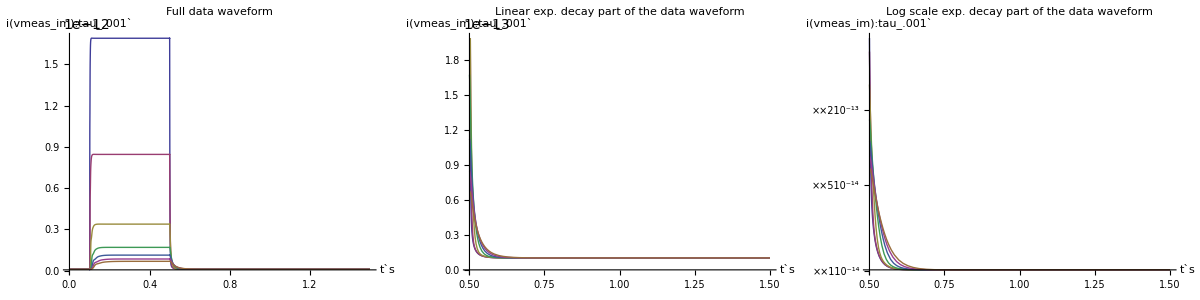
Data Waveforms
-Graphics-

```mathematica
imgSize=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[timeFilteredData,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Linear exp. decay part of the data waveform",Bold]],
ListLogPlot[timeFilteredData,AxesLabel->axesLabel,Joined->True,ImageSize->imgSize, PlotLabel->Style["Log scale exp. decay part of the data waveform",Bold]]}
}]}
}]
```

### Manipulate Data

#### Calculate τ using exponential fit including offset

```mathematica
imgSize=500;
defaultPlotNum=1;
workPrec=Automatic;
offsetLessData=validTimeFilteredData⟦plotNum⟧-offsetMins⟦plotNum⟧;
(* Extract x-values from dataset *)
xVals=Transpose[offsetLessData]⟦1⟧;
xValsExp=Transpose[validTimeFilteredData⟦defaultPlotNum⟧]⟦1⟧;
TabView[{
"Linear Log Fit"->
Manipulate[
plotNum=Sequence@@Flatten[Position[tauVals,plotID]];
offsetLessData=validTimeFilteredData⟦plotNum⟧-offsetMins⟦plotNum⟧;
xVals=Transpose[offsetLessData]⟦1⟧;
boundedOffsetLessData=Select[offsetLessData,#⟦1⟧>=lowerBound&];
boundedOffsetLessData=Select[boundedOffsetLessData,#⟦1⟧<=upperBound&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedBoundedOffsetLessData=Transpose[{boundedOffsetLessData⟦;;,1⟧-lowerBound,boundedOffsetLessData⟦;;,2⟧}];
logOffsetLessData=Transpose[{shiftedBoundedOffsetLessData⟦;;,1⟧,Log[shiftedBoundedOffsetLessData⟦;;,2⟧]}];
(*logSelData=Select[logOffsetLessData,#⟦1⟧>lowerBound&];
logSelData=Select[logSelData,#⟦1⟧<upperBound&];*)
fitLineEq=Fit[logOffsetLessData,{1,t},t];
fitLineRules=FindFit[logOffsetLessData,m t+b,{{m,-1/tauVals⟦plotNum⟧},b},t];
τ=-1/m/.fitLineRules;
errTau=Abs[τ-tauVals⟦plotNum⟧];percErrTau=(errTau/tauVals⟦plotNum⟧)*100;
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isats⟦plotNum⟧,Italic]}],
Row[{Style["Extracted Isat:  ",FontFamily->"Helvetica", Bold] ,Style[ⅇ^b/.fitLineRules,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMins⟦plotNum⟧,Italic]}]},
(*{Row[{Style["ylow:  ",FontFamily->"Helvetica", Bold] ,Style[boundedOffsetLessData⟦Position[boundedOffsetLessData,upperBound]⟦1,1⟧⟧⟦2⟧,Italic]}],
Row[{Style["yhigh:  ",FontFamily->"Helvetica", Bold] ,Style[boundedOffsetLessData⟦Position[boundedOffsetLessData,lowerBound]⟦1,1⟧⟧⟦2⟧,Italic]}]},*)
{Show[(*ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],*)
ListLogPlot[shiftedBoundedOffsetLessData,AxesLabel->axesLabel,ImageSize->imgSize,PlotRange->{{0,upperBound-lowerBound},{0,All}},PlotStyle->Red],
Plot[fitLineEq,{t,0,upperBound-lowerBound}]
],
Grid[{
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]}
}]}
}],
{{plotID,tauVals⟦defaultPlotNum⟧,"Theoretical τ Value"},tauVals},
{{lowerBound,xVals⟦10⟧,"Lower Bound"},Take[xVals,Min[40,Length[xVals]]],Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[Most[xVals]]/3]⟧,"Upper Bound"},Most[xVals]},
UnsavedVariables->{fitLineEq,fitLineRules,errTau,logOffsetLessData,boundedOffsetLessData, shiftedBoundedOffsetLessData,τ,xVals,offsetLessData,plotNum},
TrackedSymbols->{plotID,lowerBound,upperBound}
],(*Manipulate Linear *)
"Exponential Fit"->
Manipulate[
plotNum=Sequence@@Flatten[Position[tauVals,plotID]];
xValsExp=Transpose[validTimeFilteredData⟦plotNum⟧]⟦1⟧;
(* Select exponential range of data *)
selDataExp=Select[validTimeFilteredData⟦plotNum⟧,#⟦1⟧>=lowerBoundExp&];
selDataExp=Select[selDataExp,#⟦1⟧<=upperBoundExp&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedSelDataExp=Transpose[{selDataExp⟦;;,1⟧-lowerBoundExp,selDataExp⟦;;,2⟧}];
(* Find the best fit *)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[shiftedSelDataExp,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
fooCurve=NonlinearModelFit [shiftedSelDataExp,model,{a,{τexp,tauVals⟦plotNum⟧},{o,10^-14}},t,MaxIterations->10000,WorkingPrecision->workPrec];
currVals={a,o,τexp}/.fooCurveParams;
errTau=Abs[currVals⟦3⟧-tauVals⟦plotNum⟧];percErrTau=(errTau/tauVals⟦plotNum⟧)*100;
Grid[{
{Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],Row[{Style["Curve Equation:  ",FontFamily->"Helvetica", Bold] ,Style[Normal[fooCurve],Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[currVals⟦3⟧,Italic]}],
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTau,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTau,Italic]}]},
{
Show[ListPlot[shiftedSelDataExp,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Darker[Red],PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}],
Plot[fooCurve[t],{t,0,upperBoundExp-lowerBoundExp},ImageSize->imgSize,PlotRange->{{0,upperBoundExp-lowerBoundExp},{0,All}}]
],
Show[
ListLinePlot[d,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[d⟦plotNum⟧,AxesLabel->axesLabel,ImageSize->imgSize, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All},PlotStyle->Directive[Red,Thick]]
]
}(*Middle Row of Grid*)
}],
{{plotID,tauVals⟦1⟧,"Theoretical τ Value"},tauVals},
{{lowerBoundExp,xValsExp⟦10⟧,"Lower Bound"},Take[xValsExp,Min[40,Length[xValsExp]]],Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦Floor[Length[Most[xValsExp]]/3]⟧,"Upper Bound"},Most[xValsExp]},LabelStyle->Medium, 
UnsavedVariables->{model,fooCurveParams, fooCurve,currVals,errTau,selDataExp,plotNum,xValsExp},
TrackedSymbols->{plotID,lowerBoundExp,upperBoundExp}
](* Manipulate Exponential*)
},1](*TabView *)
```

12

```mathematica
MemoryInUse[]
```

47866624

### Data Analysis

#### Accuracy of Tau Values as measured from the Manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawData=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.2781, .2892, .2856, .288, .2593, .198, .1511}, {0.5, .0055, .0036, .0162, .0023, .0021, .0022, .0012}, {0.75, .0005, .0037, .0002, .0002, .00003, .0026, .0044}, {1.00, .0007, .0001, .0021, .00003, .0017, .0032, .0031}, {1.25, .0021, .0008, .0006, .0002, .0012, .0002, .0012}, {3, .0001, .0020, .0008, .00005, .0004, .0011, .0004}});
percErrTauVals=Rest[percErrTauRawData⟦1⟧];
percErriinVals=Rest[Transpose[percErrTauRawData]⟦1⟧];
percErrPlotVals=Transpose[Rest[Transpose[Rest[percErrTauRawData]]]]
MatrixPlot[percErrPlotVals,PlotRange->{0,0.3},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

(0.2781 | 0.2892 | 0.2856 | 0.288 | 0.2593 | 0.198 | 0.1511
0.0055 | 0.0036 | 0.0162 | 0.0023 | 0.0021 | 0.0022 | 0.0012
0.0005 | 0.0037 | 0.0002 | 0.0002 | 0.00003 | 0.0026 | 0.0044
0.0007 | 0.0001 | 0.0021 | 0.00003 | 0.0017 | 0.0032 | 0.0031
0.0021 | 0.0008 | 0.0006 | 0.0002 | 0.0012 | 0.0002 | 0.0012
0.0001 | 0.002 | 0.0008 | 0.00005 | 0.0004 | 0.0011 | 0.0004)

-Graphics-

## Appendix

### Calculate τ using linear fit of log of exponential decay (old method of doing this)

```mathematica
Manipulate[
dataBounds={lowerBound,upperBound};
selData=Select[timeFilteredData-offsetMin,#⟦2⟧>0&];
xVals=Transpose[selData]⟦1⟧;
logSelectedData=Transpose[{selData⟦;;,1⟧,Log[selData⟦;;,2⟧]}];
logSelData=Select[logSelectedData,#⟦1⟧>dataBounds⟦1⟧&];
logSelData=Select[logSelData,#⟦1⟧<dataBounds⟦2⟧&];
fooLine=Fit[logSelData,{1,t},t];
barLine=FindFit[logSelData,m t+b,{m,b},t];
τ=-1/m/.barLine;
Grid[{
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[Isat,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMin,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τ,Italic]}]},
{Show[ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selData,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooLine,{t,0,0.7}]
]}
}],
{{lowerBound,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBound,xVals⟦Floor[Length[xVals]/2]⟧,"Upper Bound"},xVals,Appearance->{"Labeled","Open"}}
]
```

### Playing with Exponents

#### Exponential without offset

0.1

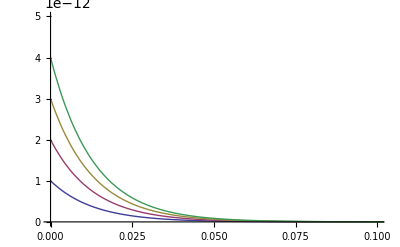

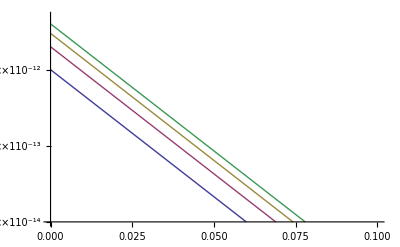

```mathematica
foo[a_,τtest_,t_]:=a*ⅇ^(-t/τtest);
a=100*10^-14;
τtest=0.013;
xMax=.1
Plot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5 a}}]
LogPlot[{foo[a,τtest,t],foo[2 a,τtest,t],foo[3 a,τtest,t],foo[4 a,τtest,t]},{t,0,1.2},
PlotRange->{{0,xMax},{a/100,5 a}}]
```

#### Exponential with offset

0.05

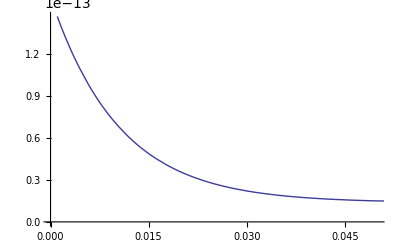

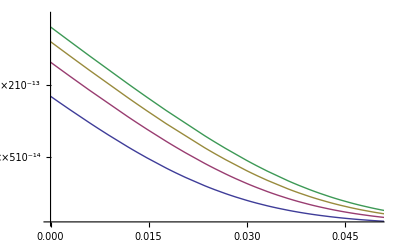

```mathematica
fooOff[a_,τtest_,t_,offset_]:=a*ⅇ^(-t/τtest)+offset;
atest=1.46548*10^-13;
τtest=0.0104876;
offsettest=1.36989*10^-14;
xMax=0.05
Plot[{fooOff[1 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,atest}}]
(*Plot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{0,5atest}}]*)
LogPlot[{fooOff[1 atest,τtest,t,offsettest],fooOff[2 atest,τtest,t,offsettest],fooOff[3 atest,τtest,t,offsettest],fooOff[4 atest,τtest,t,offsettest]},{t,0,1.2},
PlotRange->{{0,xMax},{atest/10,5atest}}]
```